# rel diff btwn cutoffs; fixed ε

## just what it sounds like. in particular explore differences for ε=10Ω.

## import data

```mathematica
basePath="C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/";
```

```mathematica
dataSharp=Import[FileNameJoin[{basePath,"pSharpvEpsilon.csv"}]];
dataExp=Import[FileNameJoin[{basePath,"pExpvEpsilon2.csv"}]];
dataGaussian=Import[FileNameJoin[{basePath,"pGaussianvEpsilon2.csv"}]];
dataLorentzian=Import[FileNameJoin[{basePath,"pLorentzianvEpsilon2.csv"}]];
```

```mathematica
pSharp=dataSharp[[All,2]];
pExp=dataExp[[All,2]];
pGaussian=dataGaussian[[All,2]];
pLorentzian=dataLorentzian[[All,2]];
```

```mathematica
pExp
```

{0.998682,0.998588,0.998508,0.998439,0.998378,0.998323,0.998273,0.998228,0.998186,0.998148,0.998112}

```mathematica
pGaussian
```

{0.998763,0.998674,0.998591,0.998516,0.998446,0.998382,0.998325,0.998272,0.998225,0.998182,0.998142}

```mathematica
pSharp
```

{0.998802,0.998745,0.998673,0.998611,0.998551,0.998482,0.998422,0.998361,0.998297,0.998241,0.998184}

```mathematica
pLorentzian
```

{0.998764,0.998676,0.998599,0.998531,0.998469,0.998413,0.998361,0.998314,0.998269,0.998228,0.99819}

## do stuff

#### exp and gaussian

```mathematica
rdExpGauss=Abs[pExp-pGaussian]/pExp
```

{0.0000813516,0.0000856187,0.0000832726,0.0000768342,0.0000684454,0.0000596532,0.0000514277,0.0000442719,0.000038356,0.0000336421,0.0000299837}

```mathematica
rdExpGauss[[6]]
```

0.0000596532

```mathematica
Abs[pExp-pGaussian]
```

{0.0000812443,0.0000854978,0.0000831484,0.0000767142,0.0000683344,0.0000595531,0.0000513389,0.0000441934,0.0000382864,0.0000335798,0.0000299271}

#### exp and sharp

```mathematica
rdExpSharp=Abs[pExp-pSharp]/pExp
```

{0.000120248,0.00015724,0.000165264,0.000172418,0.000173879,0.000159695,0.000149178,0.000133061,0.000110258,0.0000933223,0.0000716991}

```mathematica
rdExpSharp[[6]]
```

0.000159695

```mathematica
Abs[pExp-pSharp]
```

{0.000120089,0.000157018,0.000165017,0.000172149,0.000173597,0.000159427,0.000148921,0.000132825,0.000110058,0.0000931495,0.0000715638}

#### exp and lorentzian

```mathematica
rdExpLor=Abs[pExp-pLorentzian]/pExp
```

{0.000082765,0.0000880069,0.0000910669,0.0000921692,0.0000917811,0.0000903549,0.0000882595,0.0000857746,0.0000831032,0.0000803877,0.0000777248}

```mathematica
rdExpLor[[6]]
```

0.0000903549

```mathematica
Abs[pExp-pLorentzian]
```

{0.0000826559,0.0000878827,0.0000909311,0.0000920253,0.0000916322,0.0000902033,0.0000881071,0.0000856226,0.0000829525,0.0000802389,0.0000775781}

#### gaussian and sharp

```mathematica
rdGaussSharp=Abs[pGaussian-pSharp]/pGaussian
```

{0.000038893,0.0000716152,0.0000819842,0.0000955763,0.000105426,0.000100035,0.0000977454,0.0000887848,0.0000718989,0.0000596782,0.0000417141}

```mathematica
rdGaussSharp[[6]]
```

0.000100035

```mathematica
Abs[pGaussian-pSharp]
```

{0.0000388449,0.0000715202,0.0000818688,0.0000954345,0.000105262,0.0000998735,0.0000975817,0.0000886314,0.0000717713,0.0000595697,0.0000416367}

#### gaussian and lorentzian

```mathematica
rdGaussLor=Abs[pGaussian-pLorentzian]/pGaussian
```

{1.41331×10^-6,2.38802×10^-6,7.79365×10^-6,0.0000153338,0.0000233341,0.0000306999,0.0000368299,0.0000415009,0.0000447455,0.0000467441,0.0000477397}

```mathematica
rdGaussLor[[6]]
```

0.0000306999

```mathematica
Abs[pGaussian-pLorentzian]
```

{1.41156×10^-6,2.38485×10^-6,7.78267×10^-6,0.0000153111,0.0000232978,0.0000306502,0.0000367682,0.0000414292,0.0000446661,0.0000466591,0.000047651}

#### sharp and lorentzian

```mathematica
rdSharpLor=Abs[pSharp-pLorentzian]/pLorentzian
```

{0.0000374797,0.000069227,0.00007419,0.0000802413,0.00008209,0.0000693334,0.0000609132,0.0000472819,0.0000271522,0.0000129335,6.02523×10^-6}

```mathematica
rdSharpLor[[6]]
```

0.0000693334

```mathematica
Abs[pSharp-pLorentzian]
```

{0.0000374333,0.0000691353,0.0000740861,0.0000801234,0.0000819644,0.0000692233,0.0000608134,0.0000472022,0.0000271052,0.0000129106,6.01432×10^-6}

## plot this a little more nicely

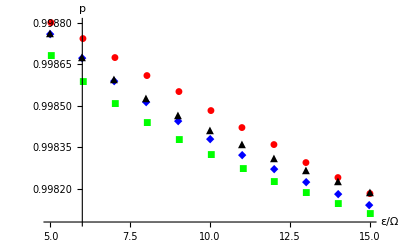

```mathematica
ListPlot[{dataSharp,dataExp,dataGaussian,dataLorentzian},
AxesLabel->{ε/Ω,p},
PlotStyle->{Red,Green,Blue,Black},
PlotMarkers->Automatic,
PlotLabel->Style["",FontSize->16]]
```